# Exercise 1.3

## Introduce a disordered interaction between next-nearest neighbours of strength W and study the band structure.

Normalizing the energy by R, the important parameter becomes the ratio W/R, which we call Μ.
Let’s start with OBC and study the bands.

```mathematica
ClearAll;
n=50;
mu=0.5; (*v/w*)
t=0.125; (*t=W/w*)
Niter=100;
p={};
e={};

For[i=0,i≤Niter,i++,

mat=Table[
If[OddQ[i],
mu*KroneckerDelta[j,i+1]+RandomReal[{-t,t}]*KroneckerDelta[j,i+2],
##&[]]
If[EvenQ[i],
1.0*KroneckerDelta[j,i+1]+RandomReal[{-t,t}]*KroneckerDelta[j,i+2],
##&[]]
,{i,1,2n},{j,1,2n}];
H=ArrayFlatten[mat + Transpose[mat]];

{energy,Cn}=Transpose[Sort[Transpose[Eigensystem[H]],#1[[1]]<#2[[1]]&]];
psi1=Cn[[n]];
psi2=Cn[[n+1]];

Pedge=psi1[[1]]^2+psi1[[2]]^2+psi1[[2n-1]]^2+psi1[[2n]]^2;  (*probability of finding the electron in the edges*)

AppendTo[e,energy];
AppendTo[p,Pedge];
]

Mean[p]
```

0.750677

{10000,2}

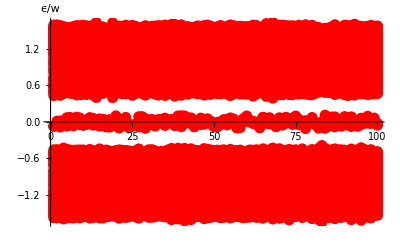

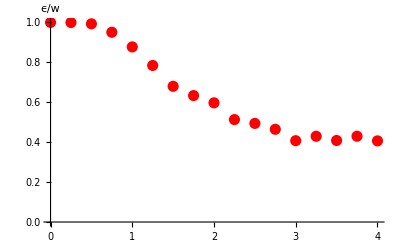

```mathematica
list={};
For[i=1,i≤Niter,i++,
For[j=1,j≤2n,j++,
AppendTo[list,{i,e[[i,j]]}]
];
]
Dimensions[list]
ListPlot[list,PlotStyle->{Red,PointSize[.02]},AxesLabel->{None,"ϵ/w"}
]
```

Let’s now study the behaviour of the band structure as a function of t in the interval [0,2].

```mathematica
ClearAll[t,mu,n,list];
mu=1.5;
n=50;
list={};
Niter=100;
dt=0.125;
t=0.0;

While[t≤2.0,

p={};

For[i=1,i≤Niter,i++,
mat=Table[
If[OddQ[i],
mu*KroneckerDelta[j,i+1]+RandomReal[{-t,t}]*KroneckerDelta[j,i+2],
##&[]]
If[EvenQ[i],
1.0*KroneckerDelta[j,i+1]+RandomReal[{-t,t}]*KroneckerDelta[j,i+2],
##&[]]
,{i,1,2n},{j,1,2n}];
H=ArrayFlatten[mat + Transpose[mat]];

{energy,Cn}=Transpose[Sort[Transpose[Eigensystem[H]],#1[[1]]<#2[[1]]&]];
psi1=Cn[[n]];
psi2=Cn[[n+1]];

Pedge=psi1[[1]]^2+psi1[[2]]^2 +psi1[[2n-1]]^2+psi1[[2n]]^2;

AppendTo[p,Pedge];
];

AppendTo[list,{t,Mean[p]}];
Clear[p];
t+=dt;
]
```

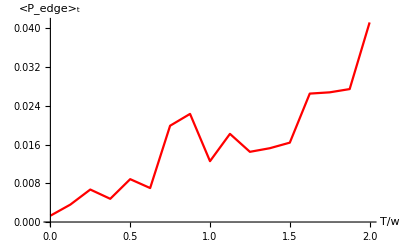

```mathematica
ListPlot[list,PlotStyle->{Red,PointSize[.015]},AxesLabel->{"T/w","<P_edge>_t"},AxesStyle->Directive[Black, 12],PlotRange->All,Joined->True]
Export["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\nnn_mu15.txt",list,"Table"];
```

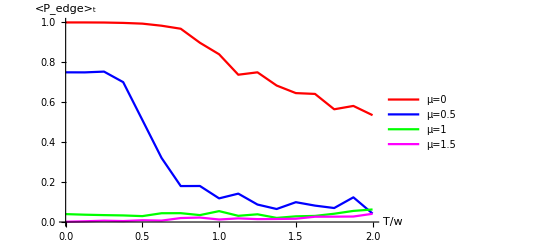

```mathematica
data0=Import["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\nnn_mu0.txt","Table"];
data05=Import["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\nnn_mu05.txt","Table"];
data1=Import["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\nnn_mu1.txt","Table"];
data15=Import["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\nnn_mu15.txt","Table"];
ListPlot[{data0,data05,data1,data15},PlotRange->All,PlotStyle->{Red,Blue,Green,Magenta},AxesLabel->{"T/w","<P_edge>_t"},AxesStyle->Directive[Black, 12],Joined->True,PlotLegends->{"μ=0","μ=0.5","μ=1","μ=1.5"}]
```